# Variance in Cellular Automata from a Biological Perspective

## Willem Nielsen

## V1

## Intro

SW and team in May 2024, now 6 months ago, published research proposing a new computational model of evolution. The idea is you start with a rule, you change the rule “one bit at a time” and you try to get the CAs to run longer and longer (not infinite), using finite length as a measure of complexity.

The basic conclusion of the experiment was that, it works: simple rules when they interact create high dimensionality. This gives evolution enough paths to get from simplicity to complexity. But, not only that, because of computational irreducibility, the paths are not correlated, so evolution doesn’t get “stuck”.

In the article SW talks about “fitness-neutral” sets: All CAs that run for the same length but get there in a different way. My idea  here, is to use these fitness-neutral sets as an analog for phenotypic variation in concurrent organisms, both within species and between species. I’m going to look at how and when these CAs adapt and  diversify and see how that relates to our understanding of how real organisms change.

In exploring this idea, I felt it was imperative to understand better how evolution played out on earth. One of the many things I learned from SW, is that you cannot untangle science from scientists. Therefore understanding evolution, means understanding how it’s discovered and by whom. One of the important figures in this story, is Charles D. Walcott.  In the summers of 1905-10, Walcott would venture from his comfortable administrative life in Washington, taking the train out west, to the paleontological sight in Western Canada, now called the Burgess Shale. After Walcott’s death, the fossils he uncovered in the Burgess Shale, turned out to be foundational evidence for the “Cambrian Explosion”.

To give you a sense of the magnitude of this discovery: “In short, Harry Whittington and his colleagues have shown that most Burgess organisms do not belong to familiar groups, and that the creatures from this single quarry in British Columbia probably exceed, in anatomical range, the entire spectrum of invertebrate life in today’s oceans. Some fifteen to twenty Burgess species cannot be allied with any known group, and should probably be classified as separate phyla.” --Stephen J. Gould

So for our purposes, here’s the basic story. For 4 billion years, we had single-cell organisms. Then BANG, we get a huge diversity of multicellular marine animals 600 million years ago. Then BANG 500 million years ago we lose a lot of that diversity in arthropods and arrive at our 4 groups today. Now, in all the records since then, we have only seen those 4 groups, and those are the groups we have today (minus trilobites who went extinct).

The point being, evolution does not crawl, it jumps. Just how fortunes can be made or lost in a day in the stock market, the fate of species can be decided in a geological day. So first of all, it’s not hard to imagine that we arrived at 4 different groups of arthropods, suggesting alien life, could be very alien indeed.

So let’s separate evolution into two dimensions. One is going from simplicity to complexity. The other one is going from uniformity to diversity. Clearly as evidence by the Burgess Shale, the speed that evolution moves along both these dimensions varies depending on the time period. It took a while to go from

To give you a sense of the importance of the Burgess Shale, there are 4 main kinds of arthropods,  in the arthropod

In doing this research one striking figure

In doing research for this article, I learned the story  of Charles Walcott’s discovery of the burgess shale.

In this article, I’m going to explore these fitness-neutral sets and try to draw some conclusions from what I find.

The focus of this article is studying their model to see “phenotypic variation”. 

Similar to how fortunes can be won and lost in a day in the stock market, evolution is dominated by a few events. As an example, It took roughly 4 billion years to go from single cell to multi-cell life.  Once it did though, within the arthro

Okay so evidence like the burgess shale shows us that diversity can evolve very rapidly, but can also disappear rapidly. The organisms seem to interact with themselves, creating winner take-all effects. Hence, why DNA is so dominant. Same goes for the arthropods. The big four won out. This is not unlike the computer revolution, where there was a window of opportunity, with lots of companies, but really the FAANG companies eventually crushed everyone.

So in the original article, SW focuses on how the CAs go from simple to complex. He touches on the concept of diversity, but I want to dive deeper here.

But the point is, that there are moments of rapid diversification, and if the CAs are indeed a good model, they will account for this. So let’s see if they do.

So, we get a sense for the diversity in the multiway graph given by SW for k=2 and r=2.

```mathematica
Graph[Module[{res,sublevels,vfs},
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,2,
GraphLayout->"LayeredDigraphEmbedding"],
"SubLevels"];
sublevels=res[[2,1,1]];
res=res[[1]];
vfs=Association[KeyValueMap[Function[{key,rules},key->GraphicsRow[
ArrayPlot[ArrayPad[#,1]&/@#,ImageSize->{Automatic,(2+key[[1]])10},Mesh->(key[[1]]<5),MeshStyle->Opacity[.1]
]&/@Union[CellularAutomaton[{#,2,2},{{1},0},
key[[1]]+1]&/@rules],Spacings->0,
PlotRangePadding->None
]],sublevels]];
ClearAttributes[vfs,Temporary];
Subgraph[res,VertexOutComponent[res,{0,1}],
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->2/3,
EdgeStyle->Gray,
VertexSize->1/2,
VertexShapeFunction->Function[
Inset[vfs[#2],#1,Automatic,
Times[#3[[1]],
#/Last[#]&@ImageDimensions[vfs[#2]],
Sqrt[First[#2]+5]
]
]
],
PerformanceGoal->"Quality"
]
],VertexCoordinates->]
```

-Graphics-

So we can see and SW points this out, that various different “ideas” are tried and there is great diversity in the shapes of automata. Not only that, but just how our human embryos look similar to a mouse. You can see families, like the line of automata that begin with black white white, circled here in green

But OK, let’s see if we can see how much diversity we can find. Looking at tri-color automata now, we accept mutations that are the most different from the current pool of organisms. The idea here, is to simulate an environment where diversity is encouraged.

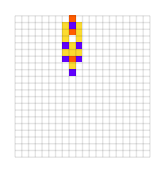
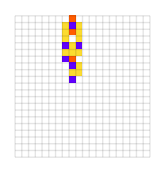
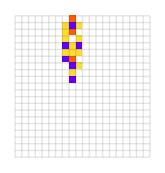
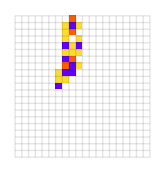
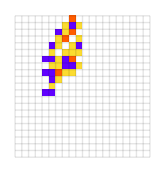
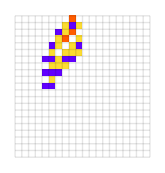
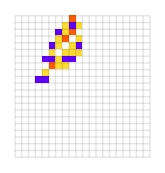
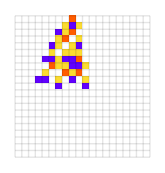

So we started with the first automata, then we just found the random mutations that maintained fitness neutrality. In this case that means they were between length 9 and 11. Of the fitness neutral automata, we select the one that has the least cells in common with all the other organisms. And what we get is this amazing array of different ways to get a length between 9 and 11. Remember this is adaptive so we mutate the most recent organism. The success of this method suggests that there are dimensions on which on can continually become more different.

An even simpler idea, is to exhaustively search the space of all fitness neutral mutations. Then we can get a broad sense of the potential flow of diversity within a fitness level. This space is too big to capture entirely even for 2 color automata, but we go 5 mutations steps deep, and we can get a sense for what’s going on.

## V2

In this blog post, Stephen Wolfram published research proposing a new computational model of evolution. The idea is you start with a rule, you change the rule “one bit at a time” and you try to get the CAs to run longer and longer (not infinite), using finite length as a measure of complexity.

The basic conclusion of the experiment was that, it works: simple rules when they interact create high dimensionality. This gives evolution enough paths to get from simplicity to complexity. But not only that, because of computational irreducibility, the paths are not correlated, so evolution doesn’t get “stuck”.

Wolfram focuses on how the CAs go from simplicity to complexity. But an equally important process, is how organisms diversify within a certain level of complexity.

There are many cases where we are interested in, not just how complex life can get, but how it changes within a certain level of complexity. Take, for example, how bacteria become resistant to antibiotics. Humans radically alter the body environment by greatly increasing the concentration of something like Penicillin. If the bacteria are lucky, then they will have a cell within their colony that say, produces an enzyme that breaks down Penicillin. That lucky bacteria will then survive and propagate the gene for that enzyme. In most cases, this doesn’t happen: antibiotics work very well. But, remarkably, in some cases, the colony survives and becomes resistant.

At its core, this resistance occurs because there is variation between the bacteria, allowing them to “find” a path to survival. Crucially, this idea of phenotypic variation, is ubiquitous among modern organisms. Not only that, but the variation is, in many cases, intentional. Meaning, we have evolved processes like sex, that maintain this variation. If we were to find life on other planets, one would bet on them having something like sex. Therefore, understanding the process of phenotypic variation will not just help us deal with our bacterial enemies, but it is at the core of understanding evolution itself.  

In light of this, I will try to, Wolfram-style, boil this process of phenotypic variation to its essential computational components. Then we will examine the behavior of these programs, looking for broad conclusions to draw. I will use Wolfram’s computational model of evolution as a starting point. In that post, Wolfram mainly focuses on the process of going from simplicity to complexity. He also discusses things like diversity of different phenotypes, the natural branching of CA patterns,  and fitness-neutral sets. He even builds a model of sexual reproduction. Here, we are concerned with the question of how variation happens from generation to generation. Therefore, I will focus on how variation can occur within a fitness neutral set. That is, a set of cellular automata that run for the same number of steps. I will use point mutation as the method of variation. As Wolfram points out, in this model, it doesn’t seem to matter much whether you use point mutations or recombination, and point mutations are much simpler to implement. Despite this, I will also explore this question and look at why point mutations may not be enough in real life.

The simplest possible thing we can do is start with an organism and search the mutations space for paths to other phenotypes of the same length.

```mathematica
vfs = Module[{mg,res,lifetimes,sublevels,sgs,vfs},
mg={{"[◼]", "MutationGraph"}}[2,3/2];
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
{"Lifetimes","SubLevels"}];
lifetimes=res[[2,1,1]];
sublevels=res[[2,2,1,1]];
sgs=Subgraph[mg,#]&/@sublevels;
vfs=Association[KeyValueMap[Function[{key,rules},key->Map[
{{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{30,Automatic}]&,
Union[CellularAutomaton[{#,2,3/2},
{{1,1,1,0,1,1,1},0},key[[1]]+1]&/@rules]]
],sublevels]];
vfs
(*Style[Row[Row[{If[VertexCount[sgs[#]]>1,Graph[sgs[#],EdgeStyle->Gray,
ImageSize->{15 VertexCount[sgs[#]]^.15,Automatic},
VertexSize->1/2/Sqrt[VertexCount[sgs[#]]+2],
VertexStyle->Directive[Lighter@Gray,EdgeForm[Opacity[.35]]],
BaselinePosition->Scaled[1/4]
],Nothing],
If[Length[vfs[#]]>3,Row[{
GraphicsRow[Take[vfs[#],3]],
Style[Row[{"… (",
Length[vfs[#]],
")"}],"Text",11,Gray]
}],
GraphicsRow[vfs[#]]]},Style[":",14,Gray]]&/@Keys[sublevels],Style[Text[" | "],20,LightGray]],LineSpacing->{1.1,0}]*)
]
```

<|{1,1}→{-Graphics-},{2,1}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{3,1}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{3,2}→{-Graphics-,-Graphics-,-Graphics-},{3,3}→{-Graphics-,-Graphics-,-Graphics-},{3,4}→{-Graphics-,-Graphics-,-Graphics-},{3,5}→{-Graphics-,-Graphics-,-Graphics-},{3,6}→{-Graphics-},{4,1}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{4,2}→{-Graphics-},{4,3}→{-Graphics-},{4,4}→{-Graphics-},{4,5}→{-Graphics-},{4,6}→{-Graphics-},{4,7}→{-Graphics-},{4,8}→{-Graphics-},{4,9}→{-Graphics-},{5,1}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{5,2}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{5,3}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{5,4}→{-Graphics-,-Graphics-},{5,5}→{-Graphics-,-Graphics-},{5,6}→{-Graphics-,-Graphics-,-Graphics-},{5,7}→{-Graphics-,-Graphics-,-Graphics-},{5,8}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{5,9}→{-Graphics-},{5,10}→{-Graphics-},{5,11}→{-Graphics-},{5,12}→{-Graphics-},{5,13}→{-Graphics-},{5,14}→{-Graphics-},{5,15}→{-Graphics-},{5,16}→{-Graphics-},{5,17}→{-Graphics-},{5,18}→{-Graphics-},{5,19}→{-Graphics-},{5,20}→{-Graphics-},{6,1}→{-Graphics-,-Graphics-},{6,2}→{-Graphics-,-Graphics-,-Graphics-},{6,3}→{-Graphics-,-Graphics-,-Graphics-},{6,4}→{-Graphics-,-Graphics-},{6,5}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{6,6}→{-Graphics-,-Graphics-},{6,7}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{6,8}→{-Graphics-},{6,9}→{-Graphics-},{6,10}→{-Graphics-},{6,11}→{-Graphics-},{6,12}→{-Graphics-},{6,13}→{-Graphics-},{7,1}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{7,2}→{-Graphics-,-Graphics-,-Graphics-},{7,3}→{-Graphics-,-Graphics-,-Graphics-},{7,4}→{-Graphics-},{7,5}→{-Graphics-},{7,6}→{-Graphics-},{7,7}→{-Graphics-},{7,8}→{-Graphics-},{7,9}→{-Graphics-},{7,10}→{-Graphics-},{7,11}→{-Graphics-},{7,12}→{-Graphics-},{8,1}→{-Graphics-},{8,2}→{-Graphics-},{8,3}→{-Graphics-},{8,4}→{-Graphics-},{8,5}→{-Graphics-},{8,6}→{-Graphics-},{8,7}→{-Graphics-},{8,8}→{-Graphics-},{8,9}→{-Graphics-},{8,10}→{-Graphics-},{9,1}→{-Graphics-},{9,2}→{-Graphics-},{9,3}→{-Graphics-},{9,4}→{-Graphics-},{9,5}→{-Graphics-},{9,6}→{-Graphics-},{9,7}→{-Graphics-},{9,8}→{-Graphics-},{9,9}→{-Graphics-},{9,10}→{-Graphics-},{9,11}→{-Graphics-},{9,12}→{-Graphics-},{10,1}→{-Graphics-},{10,2}→{-Graphics-}|>

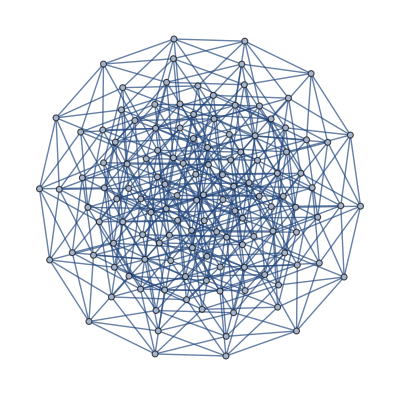
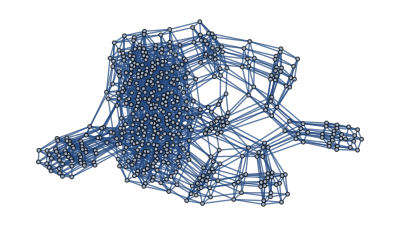
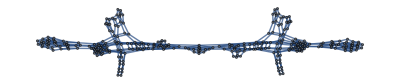
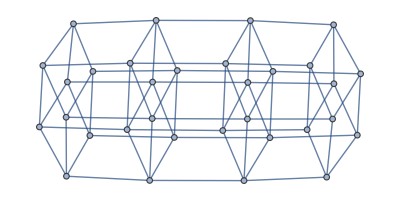
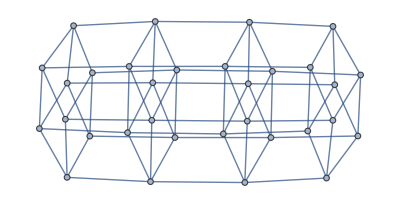
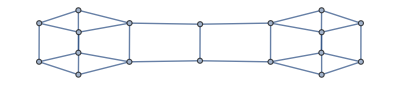
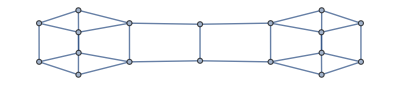
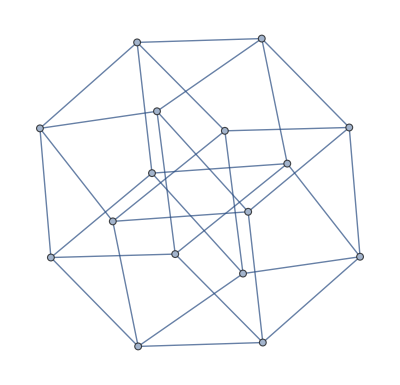

<|{1,1}→-Graphics-,{2,1}→-Graphics-,{3,1}→-Graphics-,{3,2}→-Graphics-,{3,3}→-Graphics-,{3,4}→-Graphics-,{3,5}→-Graphics-,{3,6}→-Graphics-,{4,1}→-Graphics-,{4,2}→-Graphics-,{4,3}→-Graphics-,{4,4}→-Graphics-,{4,5}→-Graphics-,{4,6}→-Graphics-,{4,7}→-Graphics-,{4,8}→-Graphics-,{4,9}→-Graphics-,{5,1}→-Graphics-,{5,2}→-Graphics-,{5,3}→-Graphics-,{5,4}→-Graphics-,{5,5}→-Graphics-,{5,6}→-Graphics-,{5,7}→-Graphics-,{5,8}→-Graphics-,{5,9}→-Graphics-,{5,10}→-Graphics-,{5,11}→-Graphics-,{5,12}→-Graphics-,{5,13}→-Graphics-,{5,14}→-Graphics-,{5,15}→-Graphics-,{5,16}→-Graphics-,{5,17}→-Graphics-,{5,18}→-Graphics-,{5,19}→-Graphics-,{5,20}→-Graphics-,{6,1}→-Graphics-,{6,2}→-Graphics-,{6,3}→-Graphics-,{6,4}→-Graphics-,{6,5}→-Graphics-,{6,6}→-Graphics-,{6,7}→-Graphics-,{6,8}→-Graphics-,{6,9}→-Graphics-,{6,10}→-Graphics-,{6,11}→-Graphics-,{6,12}→-Graphics-,{6,13}→-Graphics-,{7,1}→-Graphics-,{7,2}→-Graphics-,{7,3}→-Graphics-,{7,4}→-Graphics-,{7,5}→-Graphics-,{7,6}→-Graphics-,{7,7}→-Graphics-,{7,8}→-Graphics-,{7,9}→-Graphics-,{7,10}→-Graphics-,{7,11}→-Graphics-,{7,12}→-Graphics-,{8,1}→-Graphics-,{8,2}→-Graphics-,{8,3}→-Graphics-,{8,4}→-Graphics-,{8,5}→-Graphics-,{8,6}→-Graphics-,{8,7}→-Graphics-,{8,8}→-Graphics-,{8,9}→-Graphics-,{8,10}→-Graphics-,{9,1}→-Graphics-,{9,2}→-Graphics-,{9,3}→-Graphics-,{9,4}→-Graphics-,{9,5}→-Graphics-,{9,6}→-Graphics-,{9,7}→-Graphics-,{9,8}→-Graphics-,{9,9}→-Graphics-,{9,10}→-Graphics-,{9,11}→-Graphics-,{9,12}→-Graphics-,{10,1}→-Graphics-,{10,2}→-Graphics-|>

```mathematica
sgs = Module[{mg,res,lifetimes,sublevels,sgs,vfs},
mg={{"[◼]", "MutationGraph"}}[2,3/2];
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
{"Lifetimes","SubLevels"}];
lifetimes=res[[2,1,1]];
sublevels=res[[2,2,1,1]];
sgs=Subgraph[mg,#]&/@sublevels;
vfs=Association[KeyValueMap[Function[{key,rules},key->Map[
{{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{30,Automatic}]&,
Union[CellularAutomaton[{#,2,3/2},
{{1,1,1,0,1,1,1},0},key[[1]]+1]&/@rules]]
],sublevels]];
sgs
(*Style[Row[Row[{If[VertexCount[sgs[#]]>1,Graph[sgs[#],EdgeStyle->Gray,
ImageSize->{15 VertexCount[sgs[#]]^.15,Automatic},
VertexSize->1/2/Sqrt[VertexCount[sgs[#]]+2],
VertexStyle->Directive[Lighter@Gray,EdgeForm[Opacity[.35]]],
BaselinePosition->Scaled[1/4]
],Nothing],
If[Length[vfs[#]]>3,Row[{
GraphicsRow[Take[vfs[#],3]],
Style[Row[{"… (",
Length[vfs[#]],
")"}],"Text",11,Gray]
}],
GraphicsRow[vfs[#]]]},Style[":",14,Gray]]&/@Keys[sublevels],Style[Text[" | "],20,LightGray]],LineSpacing->{1.1,0}]*)
]
```

```mathematica
%1[{1,1}]// VertexList
```

{0,4,16,20,32,36,48,52,64,68,80,84,96,100,112,116,512,516,528,532,544,548,560,564,576,580,592,596,608,612,624,628,1024,1028,1040,1044,1056,1060,1072,1076,1088,1092,1104,1108,1120,1124,1136,1140,1536,1540,1552,1556,1568,1572,1584,1588,1600,1604,1616,1620,1632,1636,1648,1652,32768,32772,32784,32788,32800,32804,32816,32820,32832,32836,32848,32852,32864,32868,32880,32884,33280,33284,33296,33300,33312,33316,33328,33332,33344,33348,33360,33364,33376,33380,33392,33396,33792,33796,33808,33812,33824,33828,33840,33844,33856,33860,33872,33876,33888,33892,33904,33908,34304,34308,34320,34324,34336,34340,34352,34356,34368,34372,34384,34388,34400,34404,34416,34420}

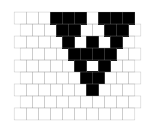
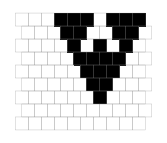
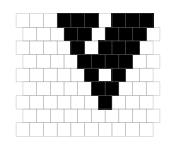
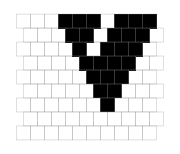
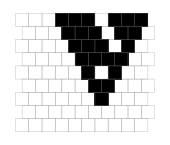
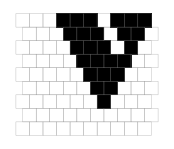
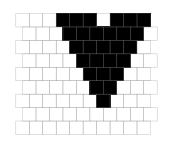

```mathematica
vfs[{7, 1}]
```

```mathematica
sgs[{7, 1}] // VertexList
```

{18144,20192,26336,50912,19680,52960,25824,59104,52448,51936,61152,58592,59072,51424,60640,60128,61120,58560,59616,60608,60096,59584}

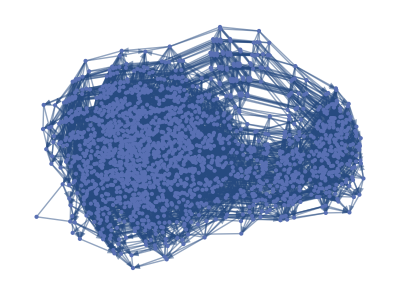

```mathematica
mg =  Module[{mg,res,lifetimes,sublevels,sgs,vfs},
mg={{"[◼]", "MutationGraph"}}[2,3/2]
(*res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
{"Lifetimes","SubLevels"}];
lifetimes=res[[2,1,1]];
sublevels=res[[2,2,1,1]]*)
(*sgs=Subgraph[mg,#]&/@sublevels;
vfs=Association[KeyValueMap[Function[{key,rules},key->Map[
{{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{30,Automatic}]&,
Union[CellularAutomaton[{#,2,3/2},
{{1,1,1,0,1,1,1},0},key[[1]]+1]&/@rules]]
],sublevels]];*)

(*Style[Row[Row[{If[VertexCount[sgs[#]]>1,Graph[sgs[#],EdgeStyle->Gray,
ImageSize->{15 VertexCount[sgs[#]]^.15,Automatic},
VertexSize->1/2/Sqrt[VertexCount[sgs[#]]+2],
VertexStyle->Directive[Lighter@Gray,EdgeForm[Opacity[.35]]],
BaselinePosition->Scaled[1/4]
],Nothing],
If[Length[vfs[#]]>3,Row[{
GraphicsRow[Take[vfs[#],3]],
Style[Row[{"… (",
Length[vfs[#]],
")"}],"Text",11,Gray]
}],
GraphicsRow[vfs[#]]]},Style[":",14,Gray]]&/@Keys[sublevels],Style[Text[" | "],20,LightGray]],LineSpacing->{1.1,0}]*)
]
```

```mathematica
sgs[{7, 1}] // VertexList
```

{18144,20192,26336,50912,19680,52960,25824,59104,52448,51936,61152,58592,59072,51424,60640,60128,61120,58560,59616,60608,60096,59584}

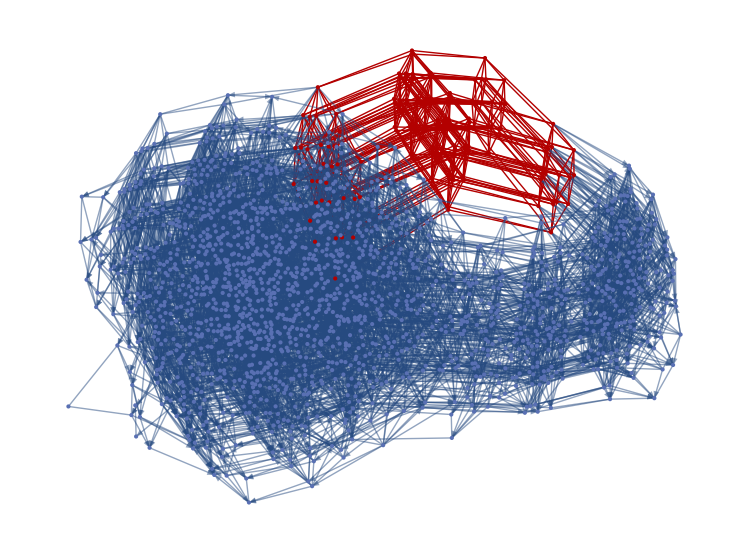

```mathematica
HighlightGraph[mg, sgs[{1, 1}]]
```

```mathematica
sls =  Module[{mg,res,lifetimes,sublevels,sgs,vfs},
mg={{"[◼]", "MutationGraph"}}[2,3/2];
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
{"Lifetimes","SubLevels"}];
lifetimes=res[[2,1,1]];
sublevels=res[[2,2,1,1]];
sgs=Subgraph[mg,#]&/@sublevels;
vfs=Association[KeyValueMap[Function[{key,rules},key->Map[
{{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{30,Automatic}]&,
Union[CellularAutomaton[{#,2,3/2},
{{1,1,1,0,1,1,1},0},key[[1]]+1]&/@rules]]
],sublevels]];
sublevels

(*Style[Row[Row[{If[VertexCount[sgs[#]]>1,Graph[sgs[#],EdgeStyle->Gray,
ImageSize->{15 VertexCount[sgs[#]]^.15,Automatic},
VertexSize->1/2/Sqrt[VertexCount[sgs[#]]+2],
VertexStyle->Directive[Lighter@Gray,EdgeForm[Opacity[.35]]],
BaselinePosition->Scaled[1/4]
],Nothing],
If[Length[vfs[#]]>3,Row[{
GraphicsRow[Take[vfs[#],3]],
Style[Row[{"… (",
Length[vfs[#]],
")"}],"Text",11,Gray]
}],
GraphicsRow[vfs[#]]]},Style[":",14,Gray]]&/@Keys[sublevels],Style[Text[" | "],20,LightGray]],LineSpacing->{1.1,0}]*)
]
```

<|{1,1}→{0,4,16,20,32,36,48,52,64,68,80,84,96,100,112,116,512,516,528,532,544,548,560,564,576,580,592,596,608,612,624,628,1024,1028,1040,1044,1056,1060,1072,1076,1088,1092,1104,1108,1120,1124,1136,1140,1536,1540,1552,1556,1568,1572,1584,1588,1600,1604,1616,1620,1632,1636,1648,1652,32768,32772,32784,32788,32800,32804,32816,32820,32832,32836,32848,32852,32864,32868,32880,32884,33280,33284,33296,33300,33312,33316,33328,33332,33344,33348,33360,33364,33376,33380,33392,33396,33792,33796,33808,33812,33824,33828,33840,33844,33856,33860,33872,33876,33888,33892,33904,33908,34304,34308,34320,34324,34336,34340,34352,34356,34368,34372,34384,34388,34400,34404,34416,34420},{2,1}→{8,40,72,104,128,160,192,224,520,552,584,616,640,672,704,736,1032,1064,1096,1128,1152,1184,1216,1248,1544,1576,1608,1640,1664,1696,1728,1760,2048,2056,2080,2088,2112,2120,2144,2152,2176,2208,2560,2568,2592,2600,2624,2632,2656,2664,3072,3080,3104,3112,3136,3144,3168,3176,3200,3232,3584,3592,3616,3624,3648,3656,3680,3688,4096,4104,4128,4136,4160,4168,4192,4200,4224,4288,4608,4616,4640,4648,4672,4680,4704,4712,4736,4800,5120,5128,5152,5160,5184,5192,5216,5224,5632,5640,5664,5672,5696,5704,5728,5736,6144,6152,6176,6184,6208,6216,6240,6248,6272,6304,7168,7176,7200,7208,7232,7240,7264,7272,8192,8200,8224,8232,8256,8264,8288,8296,8320,8384,8704,8736,8768,8800,8832,8896,9216,9224,9248,9256,9280,9288,9312,9320,9728,9760,9792,9824,10240,10244,10256,10260,10272,10276,10288,10292,10752,10756,10768,10772,10784,10788,10800,10804,11264,11268,11280,11284,11296,11300,11312,11316,11776,11780,11792,11796,11808,11812,11824,11828,12288,12296,12320,12328,12352,12360,12384,12392,12416,12480,12800,12832,12864,12896,12928,12992,13312,13320,13344,13352,13376,13384,13408,13416,13824,13856,13888,13920,16384,16392,16416,16448,16456,16480,16512,16516,16528,16532,16544,16548,16560,16564,16896,16904,16928,16960,16968,16992,17408,17440,17472,17504,17536,17540,17552,17556,17568,17572,17584,17588,17920,17952,17984,18016,18432,18440,18496,18504,18944,18952,19008,19016,24576,24584,24608,25600,25608,25632,32776,32808,32840,32872,32896,32928,32960,32992,33288,33320,33352,33384,33408,33440,33472,33504,33800,33832,33864,33896,33920,33952,33984,34016,34312,34344,34376,34408,34432,34464,34496,34528,34816,34824,34848,34856,34880,34888,34912,34920,34944,34976,35328,35336,35360,35368,35392,35400,35424,35432,35840,35848,35872,35880,35904,35912,35936,35944,35968,36000,36352,36360,36384,36392,36416,36424,36448,36456,36864,36872,36896,36904,36928,36936,36960,36968,36992,37056,37376,37384,37408,37416,37440,37448,37472,37480,37504,37568,37888,37896,37920,37928,37952,37960,37984,37992,38400,38408,38432,38440,38464,38472,38496,38504,38912,38920,38944,38952,38976,38984,39008,39016,39040,39072,39936,39944,39968,39976,40000,40008,40032,40040,40960,40968,40992,41000,41024,41032,41056,41064,41088,41152,41472,41504,41536,41568,41600,41664,41984,41992,42016,42024,42048,42056,42080,42088,42496,42528,42560,42592,43008,43012,43024,43028,43040,43044,43056,43060,43520,43524,43536,43540,43552,43556,43568,43572,44032,44036,44048,44052,44064,44068,44080,44084,44544,44548,44560,44564,44576,44580,44592,44596,45056,45064,45088,45096,45120,45128,45152,45160,45184,45248,45568,45600,45632,45664,45696,45760,46080,46088,46112,46120,46144,46152,46176,46184,46592,46624,46656,46688,49152,49160,49184,49216,49224,49248,49280,49284,49296,49300,49312,49316,49328,49332,49664,49672,49696,49728,49736,49760,50176,50208,50240,50272,50304,50308,50320,50324,50336,50340,50352,50356,50688,50720,50752,50784,51200,51208,51264,51272,51712,51720,51776,51784,57344,57352,57376,58368,58376,58400},{3,1}→{136,168,648,1160,2184,4232,8328,32904,680,1192,2216,32936,1672,4744,8840,33416,3208,33928,6280,34952,12424,37000,41096,1704,33448,3240,33960,34984,34440,12936,37512,8712,41608,35976,39048,45192,34472,36008,12808,45704,8744,8776,9736,25096,41480,12840,12872,13832,45576,8808,9768,25128,41512,9800,25160,41544,26120,42504,25088,57864,12904,13864,45608,13896,45640,46600,9832,41576,26152,42536,16936,24616,25120,57896,42568,24648,25152,57928,17928,26112,58888,25092,27136,57856,13928,45672,46632,46664,42600,25640,26144,58920,16424,17000,49704,57384,25124,27168,57888,24640,25672,57416,57920,17416,17992,50696,26116,58880,27140,57860,26624,27264,59904,46696,58408,26148,58912,16488,49192,49768,27172,57892,26656,27296,59936,24672,25664,57408,17480,58440,50184,50760,58884,26628,59908,26752,59392,10880,27328,28288,58916,49256,18980,26660,59940,26784,59424,27360,28320,25696,57440,58432,50248,59396,10368,26816,27776,2688,10896,11904,43648,28352,18468,51748,59428,26848,27808,28384,58464,10384,11392,43136,27840,2704,2720,2752,3712,6784,35456,11920,43664,44672,51236,27872,11408,43152,44160,2736,3728,35472,3744,6816,35488,2240,6848,35520,7808,36480,6656,39552,9872,44688,9360,44176,3760,35504,36496,7840,36512,4768,6688,39584,2272,3264,6336,35008,6720,39616,5760,7296,7680,40576,6664,23040,39424,42640,42128,36528,7328,7712,40608,4256,4832,37536,6696,6752,39456,3296,6368,35040,36032,39104,6728,7744,39488,5248,5824,38528,40064,7688,40448,23048,39432,20992,22528,55808,40096,7720,7776,40480,4320,37024,37600,6760,39464,39520,36064,39136,7752,39496,40512,5312,38016,38592,40456,21000,22536,55816,20480,21024,22016,53760,55296,7784,40488,40544,37088,39528,40520,38080,20488,53768,55304,20512,21504,28672,53248,22048,53792,54784,40552,28680,53256,21536,28704,53280,29696,54272,61440,54816,61448,29728,54304,61472,62464,62496},{3,2}→{8212,8244,8724,9236,24596,40980,8756,9268,24628,41012,9748,41492,25620,42004,16404,57364,9780,41524,25652,42036,16436,57396,42516,17428,58388,49172,42548,17460,58420,49204,50196,50228},{3,3}→{148,180,1172,2196,32916,1204,2228,32948,3220,33940,2068,34964,3252,33972,2100,34996,3092,35988,2580,34836,3124,36020,2612,34868,3604,35860,35348,3636,35892,35380,36372,36404},{3,4}→{16576,16608,17088,17600,49344,17632,49376,17024,49856,50368,50400,17056,18048,49792,18080,49824,50816,50848},{3,5}→{10248,10280,11272,14344,43016,11304,43048,44040,14336,47112,44072,14368,15360,47104,15392,47136,48128,48160},{3,6}→{10304,10336,10816,11328,43072,10848,11360,43104,11840,43584,44096,11872,43616,44128,44608,44640},{4,1}→{2724,19108,35492,18596,19076,19104,19124,20132,51876,43684,18564,18592,18612,19620,51364,19072,19092,20100,51844,18976,19120,20128,51872,17076,20148,51892,52900,43172,43680,43700,44708,18560,18580,19588,51332,18464,18608,19616,51360,19636,26804,51380,52388,19088,20096,23168,51840,17044,18964,20116,51860,52868,19040,20000,51744,20144,51888,52896,18100,25268,49844,52916,43168,43188,44196,10912,41632,43744,44704,44724,18576,19584,22656,51328,18452,19604,26772,51348,52356,18528,19488,51232,19632,51376,52384,27828,52404,24756,20112,51856,19968,52864,31360,18068,25236,49812,51732,52884,20064,27232,51808,20008,28192,52768,52912,26292,50868,25252,25264,58036,10400,41120,43232,44192,44212,8864,10976,11936,41696,42656,58016,35552,43712,44768,19600,51344,19456,52352,30848,51220,27796,52372,24724,19552,26720,51296,19496,27680,52256,52400,25780,24740,24752,57524,52880,20032,28160,52736,14976,31368,31392,32384,26260,50836,8852,25220,25232,58004,20072,28256,25184,27200,60000,17960,60960,26276,26288,59060,25248,58020,58032,8352,10464,11424,41184,42144,57504,43200,44256,8928,9888,2784,10944,12000,42624,59040,57984,39648,44736,52368,19520,27648,52224,14464,30856,30880,31872,25748,8340,24708,24720,57492,19560,27744,26688,59488,17448,60448,25764,25776,58548,24736,57508,57520,28224,52800,60928,14848,47744,27272,32416,26244,26256,59028,41620,25216,57988,58000,61024,57952,59968,50728,60976,26272,59044,59056,8416,9376,10432,11488,42112,58528,57472,44224,9952,9856,13984,6880,11968,42688,59008,36544,27712,52288,60416,47232,26760,31904,25732,25744,58516,41108,24704,57476,57488,60512,59456,50216,60464,25760,58532,58544,26176,60992,60944,14880,14912,15872,47616,25224,27144,27304,28296,26240,59012,26128,59024,60980,9440,9344,13472,11456,42176,58496,9920,14048,5792,3776,60480,60432,24712,26632,26792,27784,25728,58500,58512,60468,26184,58944,58896,60948,14944,15904,47648,14920,15936,47680,48640,10760,59912,28328,9408,13536,5280,38560,60436,59400,27816,58952,14952,15968,47712,48672,10824,14408,15944,48704,10792,11784,43528,38048,10856,14440,15976,48736,11848,43592,15432,47176,11816,43560,44552,11880,43624,14376,15464,47208,44616,15368,48200,44584,44648,47144,48232,48136},{4,2}→{21512,22024,54280,54792},{4,3}→{20520,21032,53288,53800},{4,4}→{5256,5768,38024,38536},{4,5}→{4264,4776,37032,37544},{4,6}→{24680,57448},{4,7}→{9752,42520},{4,8}→{7360,40128},{4,9}→{6692,39460},{5,1}→{2696,2728,3720,6792,10888,35464,3752,35496,11912,36488,14984,39560,10376,43656,36520,9864,11400,44680,14472,14856,47752,43144,9352,26248,42632,44168,47240,31240,47624,25736,42120,42664,29192,30728,31232,64008,42152,41640,29184,61960,30720,63496,31264,64000,41128,8872,29216,30208,61952,30752,63488,23072,64032,8360,25256,30240,61984,62976,22560,63520,23200,55840,24744,63008,22688,55328,56864,56352,56832,56320,24064,23552,24192,23680},{5,2}→{16916,16948,17940,25108,49684,17972,25140,49716,26132,50708,57876,20020,26164,50740,57908,28180,58900,19508,28212,52788,58932,27668,27700,52276},{5,3}→{660,692,1684,2708,33428,1716,2740,33460,3732,34452,35476,3764,9908,34484,10932,35508,36500,11956,36532,9396,42676,10420,11444,42164},{5,4}→{19464,19528,19976,27656,52232,20040,27720,52296,28168,52744,60424,28232,52808,60488,60936,61000},{5,5}→{12448,12512,12960,14496,45216,13024,14560,45280,15008,45728,47264,15072,45792,47328,47776,47840},{5,6}→{18472,18536,18984,51240,19048,26728,51304,51752,27240,51816,25192,57960},{5,7}→{7872,16064,40640,14016,15552,13504,13952,46784,13440,46272,46720,46208},{5,8}→{20616,20648,21128,21640,21672},{5,9}→{52320,52832},{5,10}→{42208,42720},{5,11}→{31880,32392},{5,12}→{30888,31400},{5,13}→{29704,62472},{5,14}→{28712,61480},{5,15}→{26208,58976},{5,16}→{18112,50880},{5,17}→{17120,49888},{5,18}→{7304,40072},{5,19}→{6312,39080},{5,20}→{3808,36576},{6,1}→{27284,27316,28308,60052,28340,60084,61076,59540,60036,60048,61108,59572,60068,60080,60564,61060,61072,59524,59536,60032,60596,61092,61104,59556,59568,60064,60548,60560,61056,59520,60580,60592,61088,59552,60544,60576},{6,2}→{23584,23712,24096,31776,24224,32288,31744,64544,32256,65056,64512,65024},{6,3}→{9384,9896,11432,25768,11944,26280,10408,44200,10920,44712,43176,43688},{6,4}→{24768,24800,25280,25792,57536,25312,57568,26304,58048,58080},{6,5}→{22568,23080,55336,55848,56360,52264,56328,23560,56840,24072},{6,6}→{18624,18656,19136,19648,51392,19168,20160,51904,52416,52928},{6,7}→{12456,12968,45224,45736,46248,46216,46240,13448,46728,13960},{6,8}→{26664,27176,59432,59944},{6,9}→{15488,16000,48256,48768},{6,10}→{26216},{6,11}→{22152},{6,12}→{21160},{6,13}→{7904},{7,1}→{18144,20192,26336,50912,19680,52960,25824,59104,52448,51936,61152,58592,59072,51424,60640,60128,61120,58560,59616,60608,60096,59584},{7,2}→{15880,32264,48648,30216,31752,65032,62984,64520},{7,3}→{6824,15016,39592,14504,14888,47784,47272,47656},{7,4}→{18484,18996,51252,51764},{7,5}→{9364,9876,42132,42644},{7,6}→{29224,61992},{7,7}→{26644,59412},{7,8}→{10388,43156},{7,9}→{7816,40584},{7,10}→{52776},{7,11}→{47688},{7,12}→{46752},{8,1}→{27688,28200,60456,60968},{8,2}→{15520,16032,48288,48800},{8,3}→{56872},{8,4}→{48712},{8,5}→{47720},{8,6}→{46760},{8,7}→{28808},{8,8}→{27156},{8,9}→{22664},{8,10}→{10900},{9,1}→{30760,31272,63528,64040},{9,2}→{15496,16008,48264,48776},{9,3}→{59496,60008},{9,4}→{48320,48832},{9,5}→{59924},{9,6}→{43668},{9,7}→{29832},{9,8}→{29320},{9,9}→{28264},{9,10}→{23176},{9,11}→{22696},{9,12}→{16096},{10,1}→{30344},{10,2}→{23208}|>

```mathematica
verts = VertexList@sgs[{7, 1}];
```

```mathematica
verts
```

{18144,20192,26336,50912,19680,52960,25824,59104,52448,51936,61152,58592,59072,51424,60640,60128,61120,58560,59616,60608,60096,59584}

```mathematica
gathered = GatherBy[verts, CellularAutomaton[{#,2,3/2},
{{1,1,1,0,1,1,1},0},8]&]
```

{{18144},{20192,19680},{26336,25824},{50912},{52960,52448,51936,51424},{59104,58592,59072,58560},{61152,60640,60128,61120,59616,60608,60096,59584}}

```mathematica
uniquecas =  CellularAutomaton[{#,2,3/2},
{{1,1,1,0,1,1,1},0},8]&/@ gathered[[All, 1]];
```

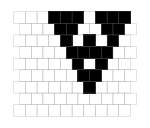
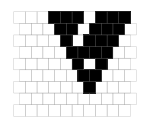
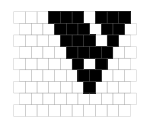
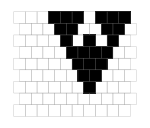
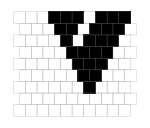
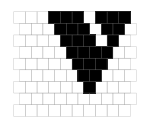
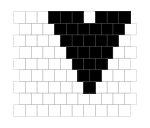

```mathematica
phenos = {{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{150,Automatic}]&/@ uniquecas
```